```mathematica
Table[ForceZero[k],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{1,1,1,1,1}

```mathematica
PushAllGraphs[]
```

0

```mathematica
PropagateAllGraphs[]
```

0

```mathematica
Table[allGraphs[k,"comp"],{k,Keys[allGraphs]}]//Tally
```

{{Greater,1844},{GreaterEqual,45},{Equal,6}}

```mathematica
counters=Association[];graphs=Association[]; Monitor[Table[
Table[If[!KeyExistsQ[counters,v],counters[v]=0;graphs[v]={}]; counters[v]=counters[v]+1;graphs[v]=Append[graphs[v],k];,{v,ListofVars[allGraphs[k,"colofour"]]}],
{k,Keys[allGraphs]}
],k]
```

{{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null},1892,{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}
 |  |  |  |

```mathematica
Values[counters]//Tally//Sort
```

{{52,1},{94,5},{138,10},{232,10},{328,15},{576,10},{1024,1}}

```mathematica
Select[Keys[counters],counters[#]==94&]
```

{v1234x5,v1235x4,v1245x3,v1345x2,v1x2345}

```mathematica
Table[Labeled[allGraphs[k,"graph"],allGraphs[k,"colofour"]],{k,Select[ graphs[v1234x5],allGraphs[#,"comp"]==Greater&]}]
```

```mathematica
Table[Labeled[allGraphs[k,"graph"],allGraphs[k,"colofour"]],{k,Select[ graphs[v13x245],allGraphs[#,"comp"]==GreaterEqual&]}]
```

{-Graphics-v13x245+v13x24x5,-Graphics-v13x245,-Graphics-v13x245+v13x25x4,-Graphics-v135x24+v13x245+v13x24x5,-Graphics-v134x25+v13x245+v13x25x4}

```mathematica
Table[Labeled[allGraphs[k,"graph"],allGraphs[k,"colofour"]],{k,Select[ graphs[allGraphs[alfa1Key,"colofour"]],allGraphs[#,"comp"]==Equal&]}]
```

{-Graphics-v13x24x5}

```mathematica
Length[atomKeys]
```

52

```mathematica
Table[Labeled[allGraphs[k,"graph"],allGraphs[k,"colofour"]],{k,Select[ graphs[allGraphs[alfa1Key,"colofour"]],allGraphs[#,"comp"]==GreaterEqual&]}]
```

{-Graphics-v13x245+v13x24x5,-Graphics-v135x24+v13x245+v13x24x5,-Graphics-v135x24+v13x24x5}

```mathematica
Table[allGraphs[k,"graph"],{k,Select[ graphs[allGraphs[alfa1Key,"colofour"]],allGraphs[#,"comp"]==Greater&]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Labeled[allGraphs[k,"graph"],Style[allGraphs[k,"colofour"]->counters[allGraphs[k,"colofour"]],ColourForKey[allGraphs,k]]],{k,Sort[atomKeys,counters[allGraphs[#1,"colofour"]]>counters[allGraphs[#2,"colofour"]]&]}]
```

{-Graphics-v1x2x3x4x5→1024,-Graphics-v12x3x4x5→576,-Graphics-v13x2x4x5→576,-Graphics-v14x2x3x5→576,-Graphics-v15x2x3x4→576,-Graphics-v1x23x4x5→576,-Graphics-v1x24x3x5→576,-Graphics-v1x25x3x4→576,-Graphics-v1x2x34x5→576,-Graphics-v1x2x35x4→576,-Graphics-v1x2x3x45→576,-Graphics-v12x34x5→328,-Graphics-v12x35x4→328,-Graphics-v12x3x45→328,-Graphics-v13x24x5→328,-Graphics-v13x25x4→328,-Graphics-v13x2x45→328,-Graphics-v14x23x5→328,-Graphics-v14x25x3→328,-Graphics-v14x2x35→328,-Graphics-v15x23x4→328,-Graphics-v15x24x3→328,-Graphics-v15x2x34→328,-Graphics-v1x23x45→328,-Graphics-v1x24x35→328,-Graphics-v1x25x34→328,-Graphics-v123x4x5→232,-Graphics-v124x3x5→232,-Graphics-v125x3x4→232,-Graphics-v134x2x5→232,-Graphics-v135x2x4→232,-Graphics-v145x2x3→232,-Graphics-v1x234x5→232,-Graphics-v1x235x4→232,-Graphics-v1x245x3→232,-Graphics-v1x2x345→232,-Graphics-v123x45→138,-Graphics-v124x35→138,-Graphics-v125x34→138,-Graphics-v12x345→138,-Graphics-v134x25→138,-Graphics-v135x24→138,-Graphics-v13x245→138,-Graphics-v145x23→138,-Graphics-v14x235→138,-Graphics-v15x234→138,-Graphics-v1234x5→94,-Graphics-v1235x4→94,-Graphics-v1245x3→94,-Graphics-v1345x2→94,-Graphics-v1x2345→94,-Graphics-v12345→52}

```mathematica
Length[Intersection[graphs[v145x23],graphs[v1x2x3x4x5]]]
```

64

```mathematica
sortedAtomKeys=Sort[atomKeys,counters[allGraphs[#1,"colofour"]]>counters[allGraphs[#2,"colofour"]]&]
```

{29524,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,49216,49210,49208,36166,36112,36086,31954,31738,31714,30496,30334,30262,29768,29608,29560,56011,51475,49963,38281,36817,32441,29857,29797,29633,29537,56012,51478,49972,49220,38308,36898,36194,32684,31984,30586,58288,56770,52232,39014,29888,59048}

```mathematica
mot=Table[With[
{set=Intersection[graphs[allGraphs[i,"colofour"]],graphs[allGraphs[j,"colofour"]]]},
(*Length[Select[set,allGraphs[#,"comp"]==GreaterEqual&]]*)Length[set]
],{i,sortedAtomKeys},{j,sortedAtomKeys}];
```

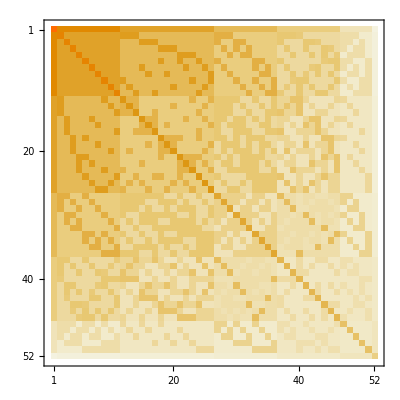

```mathematica
MatrixPlot[mot]
```

```mathematica
Product[i,{i,Flatten[mot]}]//FactorInteger
```

{{2,11212},{3,860},{5,550},{11,80},{13,31},{23,70},{29,30},{41,15},{47,5}}

```mathematica
Det[mot]//FactorInteger
```

{{2,142},{3,6},{7,7},{11,5},{13,5},{79,1},{163,4},{593,5},{619,1},{773,1},{2909,4}}

```mathematica
Tr[mot]//FactorInteger
```

{{2,1},{7963,1}}

```mathematica
Length[{{0,1}}]
```

1

```mathematica
MatrixForm[mot,TableHeadings->{Table[Graph[allGraphs[k,"graph"],ImageSize->{40,40}],{k,sortedAtomKeys}],Table[Graph[allGraphs[k,"graph"],ImageSize->{40,40}],{k,sortedAtomKeys}]},TableDepth->2]
```

( | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 1024 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 16 | 16 | 16 | 16 | 16 | 1
-Graphics- | 512 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 288 | 288 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 160 | 160 | 160 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 80 | 80 | 80 | 72 | 32 | 32 | 32 | 32 | 32 | 32 | 24 | 24 | 24 | 8 | 8 | 2
-Graphics- | 512 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 128 | 128 | 128 | 288 | 288 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 160 | 64 | 64 | 160 | 160 | 64 | 64 | 64 | 64 | 64 | 80 | 32 | 32 | 32 | 80 | 80 | 72 | 32 | 32 | 32 | 24 | 24 | 8 | 24 | 8 | 2
-Graphics- | 512 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 288 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 64 | 160 | 64 | 160 | 64 | 160 | 64 | 64 | 64 | 64 | 32 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 72 | 32 | 24 | 8 | 24 | 24 | 8 | 2
-Graphics- | 512 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 288 | 288 | 128 | 128 | 128 | 64 | 64 | 160 | 64 | 160 | 160 | 64 | 64 | 64 | 64 | 32 | 32 | 80 | 32 | 32 | 80 | 32 | 80 | 32 | 72 | 8 | 24 | 24 | 24 | 8 | 2
-Graphics- | 512 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 128 | 160 | 64 | 64 | 64 | 64 | 64 | 160 | 160 | 64 | 64 | 80 | 32 | 32 | 32 | 32 | 32 | 32 | 72 | 80 | 80 | 24 | 24 | 8 | 8 | 24 | 2
-Graphics- | 512 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 256 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 64 | 160 | 64 | 64 | 64 | 64 | 160 | 64 | 160 | 64 | 32 | 80 | 32 | 32 | 32 | 72 | 80 | 32 | 32 | 80 | 24 | 8 | 24 | 8 | 24 | 2
-Graphics- | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 256 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 64 | 64 | 160 | 64 | 64 | 64 | 64 | 160 | 160 | 64 | 32 | 32 | 80 | 32 | 72 | 32 | 80 | 32 | 80 | 32 | 8 | 24 | 24 | 8 | 24 | 2
-Graphics- | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 256 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 64 | 64 | 64 | 160 | 64 | 64 | 160 | 64 | 64 | 160 | 32 | 32 | 72 | 80 | 80 | 32 | 32 | 32 | 32 | 80 | 24 | 8 | 8 | 24 | 24 | 2
-Graphics- | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 256 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 288 | 128 | 64 | 64 | 64 | 64 | 160 | 64 | 64 | 160 | 64 | 160 | 32 | 72 | 32 | 80 | 32 | 80 | 32 | 32 | 80 | 32 | 8 | 24 | 8 | 24 | 24 | 2
-Graphics- | 512 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 256 | 576 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 64 | 64 | 64 | 64 | 64 | 160 | 64 | 64 | 160 | 160 | 72 | 32 | 32 | 80 | 32 | 32 | 80 | 80 | 32 | 32 | 8 | 8 | 24 | 24 | 24 | 2
-Graphics- | 256 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 328 | 144 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 64 | 64 | 144 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 40 | 40 | 92 | 92 | 40 | 16 | 16 | 16 | 16 | 40 | 36 | 12 | 12 | 12 | 12 | 4
-Graphics- | 256 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 144 | 328 | 144 | 64 | 64 | 64 | 64 | 64 | 144 | 64 | 64 | 64 | 64 | 144 | 64 | 80 | 80 | 80 | 32 | 80 | 32 | 32 | 80 | 32 | 80 | 40 | 92 | 40 | 92 | 16 | 40 | 16 | 16 | 40 | 16 | 12 | 36 | 12 | 12 | 12 | 4
-Graphics- | 256 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 144 | 144 | 328 | 64 | 64 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 64 | 64 | 80 | 80 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 80 | 92 | 40 | 40 | 92 | 16 | 16 | 40 | 40 | 16 | 16 | 12 | 12 | 36 | 12 | 12 | 4
-Graphics- | 256 | 128 | 288 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 64 | 64 | 64 | 328 | 144 | 144 | 64 | 64 | 64 | 64 | 144 | 64 | 64 | 144 | 64 | 80 | 80 | 32 | 80 | 80 | 32 | 80 | 32 | 80 | 32 | 40 | 40 | 16 | 16 | 40 | 92 | 92 | 16 | 16 | 40 | 36 | 12 | 12 | 12 | 12 | 4
-Graphics- | 256 | 128 | 288 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 64 | 64 | 64 | 144 | 328 | 144 | 64 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 80 | 32 | 80 | 80 | 80 | 32 | 32 | 80 | 80 | 32 | 40 | 16 | 40 | 16 | 92 | 40 | 92 | 16 | 40 | 16 | 12 | 36 | 12 | 12 | 12 | 4
-Graphics- | 256 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 64 | 64 | 144 | 144 | 144 | 328 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 64 | 64 | 80 | 32 | 32 | 80 | 80 | 80 | 32 | 32 | 80 | 80 | 92 | 16 | 16 | 40 | 40 | 40 | 92 | 40 | 16 | 16 | 12 | 12 | 12 | 36 | 12 | 4
-Graphics- | 256 | 128 | 128 | 288 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 64 | 64 | 64 | 64 | 64 | 64 | 328 | 144 | 144 | 144 | 64 | 64 | 144 | 64 | 64 | 80 | 80 | 32 | 80 | 32 | 80 | 80 | 80 | 32 | 32 | 40 | 40 | 16 | 16 | 40 | 16 | 16 | 92 | 92 | 40 | 36 | 12 | 12 | 12 | 12 | 4
-Graphics- | 256 | 128 | 128 | 288 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 64 | 64 | 64 | 64 | 144 | 64 | 144 | 328 | 144 | 64 | 64 | 64 | 64 | 64 | 144 | 32 | 80 | 80 | 80 | 32 | 80 | 32 | 80 | 80 | 32 | 16 | 40 | 40 | 16 | 92 | 16 | 40 | 40 | 92 | 16 | 12 | 12 | 36 | 12 | 12 | 4
-Graphics- | 256 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 64 | 144 | 64 | 64 | 64 | 64 | 144 | 144 | 328 | 64 | 64 | 64 | 64 | 144 | 64 | 32 | 80 | 32 | 80 | 80 | 80 | 32 | 80 | 32 | 80 | 16 | 92 | 16 | 40 | 40 | 40 | 16 | 40 | 92 | 16 | 12 | 12 | 12 | 36 | 12 | 4
-Graphics- | 256 | 128 | 128 | 128 | 288 | 288 | 128 | 128 | 128 | 128 | 128 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 64 | 64 | 328 | 144 | 144 | 144 | 64 | 64 | 80 | 32 | 80 | 32 | 80 | 80 | 80 | 80 | 32 | 32 | 40 | 16 | 40 | 16 | 16 | 40 | 16 | 92 | 40 | 92 | 12 | 36 | 12 | 12 | 12 | 4
-Graphics- | 256 | 128 | 128 | 128 | 288 | 128 | 288 | 128 | 128 | 128 | 128 | 64 | 64 | 64 | 144 | 64 | 64 | 64 | 64 | 64 | 144 | 328 | 144 | 64 | 144 | 64 | 32 | 80 | 80 | 32 | 80 | 80 | 80 | 32 | 80 | 32 | 16 | 40 | 40 | 16 | 16 | 92 | 40 | 40 | 16 | 92 | 12 | 12 | 36 | 12 | 12 | 4
-Graphics- | 256 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 288 | 128 | 128 | 144 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 144 | 144 | 328 | 64 | 64 | 144 | 32 | 32 | 80 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 16 | 16 | 92 | 40 | 40 | 40 | 16 | 40 | 16 | 92 | 12 | 12 | 12 | 36 | 12 | 4
-Graphics- | 256 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 128 | 128 | 288 | 64 | 64 | 144 | 64 | 64 | 144 | 144 | 64 | 64 | 144 | 64 | 64 | 328 | 64 | 64 | 80 | 32 | 32 | 32 | 32 | 80 | 80 | 80 | 80 | 80 | 92 | 16 | 16 | 40 | 16 | 16 | 40 | 92 | 40 | 40 | 12 | 12 | 12 | 12 | 36 | 4
-Graphics- | 256 | 128 | 128 | 128 | 128 | 128 | 288 | 128 | 128 | 288 | 128 | 64 | 144 | 64 | 144 | 64 | 64 | 64 | 64 | 144 | 64 | 144 | 64 | 64 | 328 | 64 | 32 | 80 | 32 | 32 | 80 | 32 | 80 | 80 | 80 | 80 | 16 | 92 | 16 | 40 | 16 | 92 | 40 | 16 | 40 | 40 | 12 | 12 | 12 | 12 | 36 | 4
-Graphics- | 256 | 128 | 128 | 128 | 128 | 128 | 128 | 288 | 288 | 128 | 128 | 144 | 64 | 64 | 64 | 144 | 64 | 64 | 144 | 64 | 64 | 64 | 144 | 64 | 64 | 328 | 32 | 32 | 80 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 16 | 16 | 92 | 40 | 92 | 16 | 40 | 16 | 40 | 40 | 12 | 12 | 12 | 12 | 36 | 4
-Graphics- | 128 | 160 | 160 | 64 | 64 | 160 | 64 | 64 | 64 | 64 | 64 | 80 | 80 | 80 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 32 | 32 | 232 | 48 | 48 | 48 | 48 | 16 | 48 | 48 | 16 | 16 | 116 | 24 | 24 | 20 | 24 | 24 | 20 | 20 | 24 | 24 | 44 | 44 | 8 | 8 | 8 | 5
-Graphics- | 128 | 160 | 64 | 160 | 64 | 64 | 160 | 64 | 64 | 64 | 64 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 80 | 80 | 32 | 80 | 32 | 32 | 80 | 32 | 48 | 232 | 48 | 48 | 16 | 48 | 48 | 16 | 48 | 16 | 24 | 116 | 24 | 20 | 24 | 20 | 24 | 24 | 20 | 24 | 44 | 8 | 44 | 8 | 8 | 5
-Graphics- | 128 | 160 | 64 | 64 | 160 | 64 | 64 | 160 | 64 | 64 | 64 | 80 | 80 | 80 | 32 | 80 | 32 | 32 | 80 | 32 | 80 | 80 | 80 | 32 | 32 | 80 | 48 | 48 | 232 | 16 | 48 | 48 | 16 | 48 | 48 | 16 | 24 | 24 | 116 | 20 | 20 | 24 | 24 | 24 | 24 | 20 | 8 | 44 | 44 | 8 | 8 | 5
-Graphics- | 128 | 64 | 160 | 160 | 64 | 64 | 64 | 64 | 160 | 64 | 64 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 48 | 48 | 16 | 232 | 48 | 48 | 48 | 16 | 16 | 48 | 24 | 24 | 20 | 24 | 116 | 24 | 20 | 24 | 20 | 24 | 44 | 8 | 8 | 44 | 8 | 5
-Graphics- | 128 | 64 | 160 | 64 | 160 | 64 | 64 | 64 | 64 | 160 | 64 | 32 | 80 | 32 | 80 | 80 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 32 | 80 | 32 | 48 | 16 | 48 | 48 | 232 | 48 | 16 | 48 | 16 | 48 | 24 | 20 | 24 | 24 | 24 | 116 | 20 | 24 | 24 | 20 | 8 | 44 | 8 | 44 | 8 | 5
-Graphics- | 128 | 64 | 64 | 160 | 160 | 64 | 64 | 64 | 64 | 64 | 160 | 32 | 32 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 80 | 80 | 80 | 80 | 32 | 32 | 16 | 48 | 48 | 48 | 48 | 232 | 16 | 16 | 48 | 48 | 20 | 24 | 24 | 24 | 24 | 24 | 24 | 116 | 20 | 20 | 8 | 8 | 44 | 44 | 8 | 5
-Graphics- | 128 | 64 | 64 | 64 | 64 | 160 | 160 | 64 | 160 | 64 | 64 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 80 | 80 | 48 | 48 | 16 | 48 | 16 | 16 | 232 | 48 | 48 | 48 | 24 | 24 | 20 | 24 | 24 | 20 | 24 | 20 | 24 | 116 | 44 | 8 | 8 | 8 | 44 | 5
-Graphics- | 128 | 64 | 64 | 64 | 64 | 160 | 64 | 160 | 64 | 160 | 64 | 32 | 80 | 32 | 32 | 80 | 32 | 80 | 80 | 80 | 80 | 32 | 32 | 80 | 80 | 80 | 48 | 16 | 48 | 16 | 48 | 16 | 48 | 232 | 48 | 48 | 24 | 20 | 24 | 24 | 20 | 24 | 24 | 20 | 116 | 24 | 8 | 44 | 8 | 8 | 44 | 5
-Graphics- | 128 | 64 | 64 | 64 | 64 | 64 | 160 | 160 | 64 | 64 | 160 | 32 | 32 | 80 | 80 | 80 | 80 | 32 | 80 | 32 | 32 | 80 | 32 | 80 | 80 | 80 | 16 | 48 | 48 | 16 | 16 | 48 | 48 | 48 | 232 | 48 | 20 | 24 | 24 | 24 | 20 | 20 | 116 | 24 | 24 | 24 | 8 | 8 | 44 | 8 | 44 | 5
-Graphics- | 128 | 64 | 64 | 64 | 64 | 64 | 64 | 64 | 160 | 160 | 160 | 80 | 80 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 80 | 80 | 80 | 16 | 16 | 16 | 48 | 48 | 48 | 48 | 48 | 48 | 232 | 20 | 20 | 20 | 116 | 24 | 24 | 24 | 24 | 24 | 24 | 8 | 8 | 8 | 44 | 44 | 5
-Graphics- | 64 | 80 | 80 | 32 | 32 | 80 | 32 | 32 | 32 | 32 | 72 | 40 | 40 | 92 | 40 | 40 | 92 | 40 | 16 | 16 | 40 | 16 | 16 | 92 | 16 | 16 | 116 | 24 | 24 | 24 | 24 | 20 | 24 | 24 | 20 | 20 | 138 | 12 | 12 | 26 | 12 | 12 | 26 | 26 | 12 | 12 | 22 | 22 | 12 | 12 | 12 | 10
-Graphics- | 64 | 80 | 32 | 80 | 32 | 32 | 80 | 32 | 32 | 72 | 32 | 40 | 92 | 40 | 40 | 16 | 16 | 40 | 40 | 92 | 16 | 40 | 16 | 16 | 92 | 16 | 24 | 116 | 24 | 24 | 20 | 24 | 24 | 20 | 24 | 20 | 12 | 138 | 12 | 26 | 12 | 26 | 12 | 12 | 26 | 12 | 22 | 12 | 22 | 12 | 12 | 10
-Graphics- | 64 | 80 | 32 | 32 | 80 | 32 | 32 | 80 | 72 | 32 | 32 | 92 | 40 | 40 | 16 | 40 | 16 | 16 | 40 | 16 | 40 | 40 | 92 | 16 | 16 | 92 | 24 | 24 | 116 | 20 | 24 | 24 | 20 | 24 | 24 | 20 | 12 | 12 | 138 | 26 | 26 | 12 | 12 | 12 | 12 | 26 | 12 | 22 | 22 | 12 | 12 | 10
-Graphics- | 64 | 72 | 32 | 32 | 32 | 32 | 32 | 32 | 80 | 80 | 80 | 92 | 92 | 92 | 16 | 16 | 40 | 16 | 16 | 40 | 16 | 16 | 40 | 40 | 40 | 40 | 20 | 20 | 20 | 24 | 24 | 24 | 24 | 24 | 24 | 116 | 26 | 26 | 26 | 138 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 22 | 22 | 10
-Graphics- | 64 | 32 | 80 | 80 | 32 | 32 | 32 | 72 | 80 | 32 | 32 | 40 | 16 | 16 | 40 | 92 | 40 | 40 | 92 | 40 | 16 | 16 | 40 | 16 | 16 | 92 | 24 | 24 | 20 | 116 | 24 | 24 | 24 | 20 | 20 | 24 | 12 | 12 | 26 | 12 | 138 | 12 | 26 | 12 | 26 | 12 | 22 | 12 | 12 | 22 | 12 | 10
-Graphics- | 64 | 32 | 80 | 32 | 80 | 32 | 72 | 32 | 32 | 80 | 32 | 16 | 40 | 16 | 92 | 40 | 40 | 16 | 16 | 40 | 40 | 92 | 40 | 16 | 92 | 16 | 24 | 20 | 24 | 24 | 116 | 24 | 20 | 24 | 20 | 24 | 12 | 26 | 12 | 12 | 12 | 138 | 26 | 12 | 12 | 26 | 12 | 22 | 12 | 22 | 12 | 10
-Graphics- | 64 | 32 | 72 | 32 | 32 | 32 | 80 | 80 | 32 | 32 | 80 | 16 | 16 | 40 | 92 | 92 | 92 | 16 | 40 | 16 | 16 | 40 | 16 | 40 | 40 | 40 | 20 | 24 | 24 | 20 | 20 | 24 | 24 | 24 | 116 | 24 | 26 | 12 | 12 | 12 | 26 | 26 | 138 | 12 | 12 | 12 | 12 | 12 | 22 | 12 | 22 | 10
-Graphics- | 64 | 32 | 32 | 80 | 80 | 72 | 32 | 32 | 32 | 32 | 80 | 16 | 16 | 40 | 16 | 16 | 40 | 92 | 40 | 40 | 92 | 40 | 40 | 92 | 16 | 16 | 20 | 24 | 24 | 24 | 24 | 116 | 20 | 20 | 24 | 24 | 26 | 12 | 12 | 12 | 12 | 12 | 12 | 138 | 26 | 26 | 12 | 12 | 22 | 22 | 12 | 10
-Graphics- | 64 | 32 | 32 | 72 | 32 | 80 | 32 | 80 | 32 | 80 | 32 | 16 | 40 | 16 | 16 | 40 | 16 | 92 | 92 | 92 | 40 | 16 | 16 | 40 | 40 | 40 | 24 | 20 | 24 | 20 | 24 | 20 | 24 | 116 | 24 | 24 | 12 | 26 | 12 | 12 | 26 | 12 | 12 | 26 | 138 | 12 | 12 | 22 | 12 | 12 | 22 | 10
-Graphics- | 64 | 32 | 32 | 32 | 72 | 80 | 80 | 32 | 80 | 32 | 32 | 40 | 16 | 16 | 40 | 16 | 16 | 40 | 16 | 16 | 92 | 92 | 92 | 40 | 40 | 40 | 24 | 24 | 20 | 24 | 20 | 20 | 116 | 24 | 24 | 24 | 12 | 12 | 26 | 12 | 12 | 26 | 12 | 26 | 12 | 138 | 22 | 12 | 12 | 12 | 22 | 10
-Graphics- | 16 | 24 | 24 | 24 | 8 | 24 | 24 | 8 | 24 | 8 | 8 | 36 | 12 | 12 | 36 | 12 | 12 | 36 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 44 | 44 | 8 | 44 | 8 | 8 | 44 | 8 | 8 | 8 | 22 | 22 | 12 | 12 | 22 | 12 | 12 | 12 | 12 | 22 | 94 | 10 | 10 | 10 | 10 | 15
-Graphics- | 16 | 24 | 24 | 8 | 24 | 24 | 8 | 24 | 8 | 24 | 8 | 12 | 36 | 12 | 12 | 36 | 12 | 12 | 12 | 12 | 36 | 12 | 12 | 12 | 12 | 12 | 44 | 8 | 44 | 8 | 44 | 8 | 8 | 44 | 8 | 8 | 22 | 12 | 22 | 12 | 12 | 22 | 12 | 12 | 22 | 12 | 10 | 94 | 10 | 10 | 10 | 15
-Graphics- | 16 | 24 | 8 | 24 | 24 | 8 | 24 | 24 | 8 | 8 | 24 | 12 | 12 | 36 | 12 | 12 | 12 | 12 | 36 | 12 | 12 | 36 | 12 | 12 | 12 | 12 | 8 | 44 | 44 | 8 | 8 | 44 | 8 | 8 | 44 | 8 | 12 | 22 | 22 | 12 | 12 | 12 | 22 | 22 | 12 | 12 | 10 | 10 | 94 | 10 | 10 | 15
-Graphics- | 16 | 8 | 24 | 24 | 24 | 8 | 8 | 8 | 24 | 24 | 24 | 12 | 12 | 12 | 12 | 12 | 36 | 12 | 12 | 36 | 12 | 12 | 36 | 12 | 12 | 12 | 8 | 8 | 8 | 44 | 44 | 44 | 8 | 8 | 8 | 44 | 12 | 12 | 12 | 22 | 22 | 22 | 12 | 22 | 12 | 12 | 10 | 10 | 10 | 94 | 10 | 15
-Graphics- | 16 | 8 | 8 | 8 | 8 | 24 | 24 | 24 | 24 | 24 | 24 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 12 | 36 | 36 | 36 | 8 | 8 | 8 | 8 | 8 | 8 | 44 | 44 | 44 | 44 | 12 | 12 | 12 | 22 | 12 | 12 | 22 | 12 | 22 | 22 | 10 | 10 | 10 | 10 | 94 | 15
-Graphics- | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 5 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 10 | 15 | 15 | 15 | 15 | 15 | 52)

```mathematica
52*52
```

2704

```mathematica
shortGraphs=Select[allGraphs,Length[ListofVars[#["colofour"]]]==2&];
```

```mathematica
Length[shortGraphs]
```

160

```mathematica
Sort[Table[Labeled[allGraphs[i,"graph"],Style[i,ColourForKey[allGraphs,i]]]->Length[Select[shortGraphs,With[{l=ListofVars[#["colofour"]]},Length[l]==2&& MemberQ[l,allGraphs[i,"colofour"]]]&]],{i,sortedAtomKeys}],#1[[2]]>#2[[2]]&]
```

{-Graphics-59048→15,-Graphics-29524→10,-Graphics-29888→8,-Graphics-39014→8,-Graphics-52232→8,-Graphics-56770→8,-Graphics-58288→8,-Graphics-29525→7,-Graphics-29527→7,-Graphics-29533→7,-Graphics-29551→7,-Graphics-29605→7,-Graphics-29767→7,-Graphics-30253→7,-Graphics-31711→7,-Graphics-36085→7,-Graphics-49207→7,-Graphics-29537→6,-Graphics-29633→6,-Graphics-29797→6,-Graphics-29857→6,-Graphics-32441→6,-Graphics-36817→6,-Graphics-38281→6,-Graphics-49963→6,-Graphics-51475→6,-Graphics-56011→6,-Graphics-30586→5,-Graphics-31984→5,-Graphics-32684→5,-Graphics-36194→5,-Graphics-36898→5,-Graphics-38308→5,-Graphics-49220→5,-Graphics-49972→5,-Graphics-51478→5,-Graphics-56012→5,-Graphics-29560→5,-Graphics-29608→5,-Graphics-29768→5,-Graphics-30262→5,-Graphics-30334→5,-Graphics-30496→5,-Graphics-31714→5,-Graphics-31738→5,-Graphics-31954→5,-Graphics-36086→5,-Graphics-36112→5,-Graphics-36166→5,-Graphics-49208→5,-Graphics-49210→5,-Graphics-49216→5}

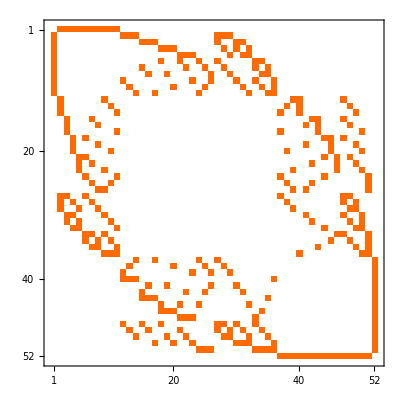

```mathematica
MatrixPlot[Table[Length[Select[shortGraphs,(#["colofour"]==allGraphs[i,"colofour"]+allGraphs[j,"colofour"])&]],{i,sortedAtomKeys},{j,sortedAtomKeys}]]
```

```mathematica
mot2=Table[Length[Select[shortGraphs,(#["colofour"]==allGraphs[i,"colofour"]+allGraphs[j,"colofour"])/.repZero&]],{i,sortedAtomKeys},{j,sortedAtomKeys}];
```

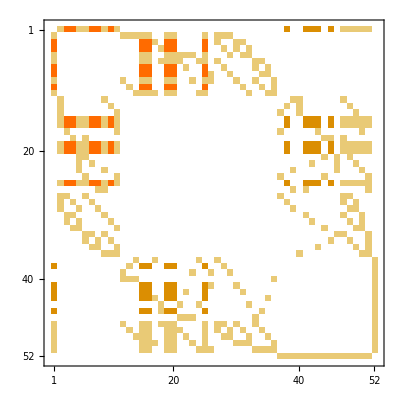

```mathematica
MatrixPlot[mot2]
```